```mathematica
WNfull[n_]:=-12/(n-n^3);
WNasym[n_]:=12/n^3;
ARfull[n_,a_]:=-1/((-1+a)^4 n^2 (-1+n^2)^2)12 (6 a^(3+n) (-1+n)^2+n-n^3+6 a^(1+n) (1+n)^2-12 a^(2+n) (-1+n^2)+a^4 n (-1+n^2)-12 a^2 (1+n^2)-2 a^3 (3-n-3 n^2+n^3)+2 a (-3-n+3 n^2+n^3));
ARasym[n_,a_]:=12*(1+a)/(1-a)*n^(-3);
ARF0d0full[n_,d_]:=(12 ((-1+d) (3 n (-1+n^2)+2 d^2 n (-2-3 n+2 n^2)+d (3-8 n-9 n^2+8 n^3)) Gamma[1-d] Gamma[1+d] Gamma[1-d+n]+Gamma[2-d] (d (3+8 d+4 d^2) n (-1+n^2) Gamma[d] Gamma[1-d+n]+3 (d^2-n^2-d^2 n^2+2 d^3 n^2+n^4-2 d n^4) Gamma[1-d] Gamma[d+n])))/(d (1+2 d) (3+2 d) n^2 (-1+n^2)^2 Gamma[2-d] Gamma[d] Gamma[1-d+n]);
ARF0d0asym[n_,d_]:=(36 (1-2 d) Gamma[1-d])/(d (1+2 d) (3+2 d) Gamma[d])*n^(2*d-3);
ARF1d0full[n_,a_,d_]:=(12 (1-a^2) (-(-1+a)^2 (-1+a^2) n (-1+n^2) Gamma[1-d] Gamma[-d+n] ((2 d^3 n (2+3 n-2 n^2)+3 n (-1+n^2)+d^2 (-3+4 n+3 n^2-4 n^3)+d (3-5 n-9 n^2+5 n^3)) Gamma[1+d] Gamma[1-d+n]-3 (d^2-n^2-d^2 n^2+2 d^3 n^2+n^4-2 d n^4) Gamma[2-d] Gamma[d+n])-(-1+a)^4 d (1+2 d) (3+2 d) n^2 (-1+n^2)^2 Gamma[2-d] Gamma[d] Gamma[-d+n] Gamma[1-d+n] (-1+2 Hypergeometric2F1[1,d,1-d,a])-2 (-1+a)^2 a d (1+2 d) (3+2 d) (-1+n)^2 n (1+n) Gamma[-d+n] (-n (1+n) Gamma[1-d] Gamma[1+d] Gamma[1-d+n] (-1+Hypergeometric2F1[1,-1+d,-d,a]+Hypergeometric2F1[1,1+d,2-d,a])+Gamma[2-d] ((-3-2 n+n^2) Gamma[d] Gamma[1-d+n] (-1+2 Hypergeometric2F1[1,d,1-d,a])-3 (-1+n) Gamma[1-d] Gamma[d+n] (-1+Hypergeometric2F1[1,d-n,1-d-n,a]+Hypergeometric2F1[1,d+n,1-d+n,a])))-12 a d (3+2 d) (n-n^3) ((-1+a^2) Gamma[1-d] Gamma[-d+n] ((-1+d) Gamma[1+d] Gamma[1-d+n]-(d-n) (-1+2 n) Gamma[2-d] Gamma[d+n])+2 a (1+2 d) Gamma[2-d] (Gamma[d] Gamma[-d+n] Gamma[1-d+n] (1-2 Hypergeometric2F1[1,d,1-d,a])+n Gamma[1-d] Gamma[1-d+n] Gamma[-1+d+n] (-1+Hypergeometric2F1[1,1+d-n,2-d-n,a]+Hypergeometric2F1[1,-1+d+n,-d+n,a])-(-1+n) Gamma[1-d] Gamma[-d+n] Gamma[d+n] (-1+Hypergeometric2F1[1,d-n,1-d-n,a]+Hypergeometric2F1[1,d+n,1-d+n,a])))))/((-1+a)^4 (-1+a^2) d (1+2 d) (3+2 d) n^3 (-1+n^2)^3 Gamma[2-d] Gamma[d] Gamma[-d+n] Gamma[1-d+n] (-1+2 Hypergeometric2F1[1,d,1-d,a]));
ARF1d0asym[n_,a_,d_]:=(-(18 ((-1+a^2) (1-2 d) Gamma[1-d]))/(d (1+2 d) (3+2 d) Gamma[d] (-1+2 Hypergeometric2F1[1,d,1-d,a])))*(2/(1-a)^2)*n^(2*d-3);
```

General::munfl: Exp[-681.803-521.504 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-682.825-521.504 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Divide::indet: Indeterminate expression 0./0. encountered.

General::stop: Further output of Divide::indet will be suppressed during this calculation.

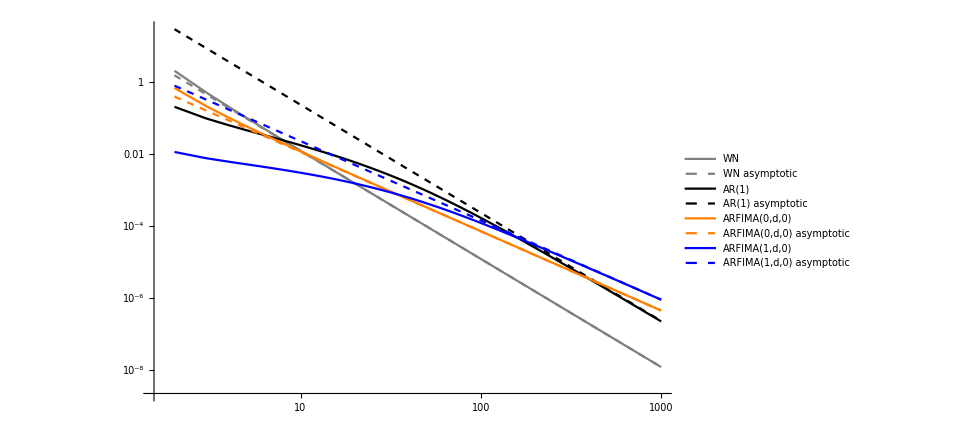

```mathematica
a=0.9;
d=0.4;
nmax=1000;
ListLogLogPlot[{
Table[WNfull[n],{n,2,nmax}],
Table[WNasym[n],{n,2,nmax}],
Table[ARfull[n,a],{n,2,nmax}],
Table[ARasym[n,a],{n,2,nmax}],
Table[ARF0d0full[n,d],{n,2,nmax}],
Table[ARF0d0asym[n,d],{n,2,nmax}],
Table[ARF1d0full[n,a,d],{n,2,nmax}],
Table[ARF1d0asym[n,a,d],{n,2,nmax}]
},
PlotLegends->Placed[{"WN","WN asymptotic","AR(1)","AR(1) asymptotic","ARFIMA(0,d,0)","ARFIMA(0,d,0) asymptotic","ARFIMA(1,d,0)","ARFIMA(1,d,0) asymptotic"},{Scaled[{0.05,0.1}],{0,0}}],
PlotStyle->{Gray,{Gray,Dashed},Black,{Black,Dashed},Orange,{Orange,Dashed},Blue,{Blue,Dashed}},
Joined->True,
LabelStyle->Directive[FontSize->14,FontFamily->"FontStyle"],
DataRange->{2,nmax}]
Clear[a]
Clear[d]
```

```mathematica
a=0.95;
d=0.45;
data = Table[ARF1d0full[n,a,d],{n,5,1500}]
Export["/Users/tphillips/Atmospheric time series/arfima1d0_closed3.txt",data,"Table"]
```

General::munfl: Exp[-682.096-521.504 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-682.607-521.504 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Divide::indet: Indeterminate expression 0./0. encountered.

General::stop: Further output of Divide::indet will be suppressed during this calculation.

{0.000785995,0.000715099,0.000659292,0.000613339,0.000574357,0.000540585,0.000510863,0.000484382,0.000460557,0.00043895,0.000419223,0.00040111,0.000384397,0.000368911,0.000354508,0.000341069,0.000328492,0.000316692,0.000305593,0.000295132,0.000285253,0.000275906,0.000267048,0.000258641,0.000250651,0.000243047,0.000235802,0.00022889,0.00022229,0.00021598,0.000209943,0.000204162,0.00019862,0.000193305,0.000188202,0.0001833,0.000178588,0.000174055,0.000169692,0.000165491,0.000161441,0.000157537,0.000153771,0.000150136,0.000146626,0.000143236,0.000139958,0.00013679,0.000133725,0.000130758,0.000127887,0.000125106,0.000122412,0.000119801,0.00011727,0.000114815,0.000112434,0.000110123,0.00010788,0.000105702,0.000103587,0.000101532,0.0000995348,0.0000975934,0.0000957058,0.0000938699,0.000092084,0.0000903463,0.000088655,0.0000870085,0.0000854053,0.0000838439,0.0000823229,0.0000808409,0.0000793966,0.0000779887,0.0000766162,0.0000752777,0.0000739723,0.0000726988,0.0000714563,0.0000702437,0.0000690602,0.0000679049,0.0000667768,0.0000656751,0.0000645991,0.000063548,0.000062521,0.0000615174,0.0000605366,0.0000595778,0.0000586404532746533,0.0000577239061297934,0.000056827574205735,0.0000559508838115059,0.0000550932813053114,0.0000542542322436138,0.0000534332205893121,0.0000526297479480136,0.0000518433328419918,0.000051073510023898,0.0000503198298217584,0.0000495818575127872,0.0000488591727290204,0.0000481513688910978,0.0000474580526667624,0.0000467788434579346,0.0000461133729024242,0.0000454612844122224,0.000044822232719113,0.0000441958834481855,0.0000435819127093642,0.0000429800067045165,0.0000423898613539395,0.0000418111819380202,0.0000412436827547138,0.0000406870867923612,0.0000401411254142397,0.0000396055380594534,0.0000390800719538272,0.0000385644818340111,0.0000380585296829134,0.0000375619844761672,0.0000370746219381849,0.0000365962243086429,0.0000361265801189849,0.0000356654839761021,0.0000352127363570829,0.0000347681434099108,0.0000343315167627225,0.0000339026733411803,0.0000334814351919683,0.0000330676293142359,0.0000326610874952037,0.0000322616461554718,0.0000318691461974056,0.0000314834328602801,0.0000311043555803627,0.0000307317678578527,0.000030365527125955,0.0000300054946275484,0.0000296515352944717,0.0000293035176318741,0.0000289613136077902,0.0000286247985437661,0.0000282938510136962,0.0000279683527417302,0.0000276481885073453,0.0000273332460521489,0.0000270234159896178,0.0000267185917194816,0.0000264186693434843,0.000026123547584957,0.0000258331277112874,0.0000255473134582956,0.0000252660109577182,0.0000249891286672387,0.0000247165773025425,0.000024448269771754,0.0000241841211123318,0.0000239240484295527,0.0000236679708376038,0.0000234158094020592,0.0000231674870848908,0.0000229229286905603,0.0000226820608142889,0.000022444811792106,0.0000222111116791469,0.0000219808949564516,0.0000217542950325966,0.0000215202576116809,0.0000136966393044059,0.0000295251430193929,0.0000208797206052679,0.0000206690360763336,0.000020461396239058,0.0000202567444068404,0.0000200550251767498,0.0000198561843960888,0.0000196601691283327,0.0000194669276219324,0.0000192764092782902,0.0000190885646222569,0.0000189033452725793,0.0000187207039132883,0.0000185405942664813,0.0000183629710654884,0.0000181877900286018,0.0000180150078343273,0.0000178445820966757,0.0000176764713414821,0.0000175106349833603,0.0000173470333033732,0.0000171856274271439,0.0000170263793039753,0.0000168692516862545,0.0000167142081093625,0.0000165612128727043,0.0000164102310205353,0.0000162612283239749,0.0000161141712630333,0.0000159690270094329,0.0000158257634100267,0.0000156843489701638,0.0000155447528379539,0.0000154069447891087,0.0000152708952114544,0.0000151365750908143,0.0000150039559965491,0.0000148730100678231,0.0000147437100003552,0.0000146160290328555,0.000014489940935126,0.0000143654199948406,0.0000142424410061013,0.0000141209792574412,0.0000140010105205029,0.0000138825110390106,0.0000137654575177373,0.0000136498271121989,0.0000135355974182731,0.0000134227464623308,0.0000133112526913822,0.0000132010949636787,0.0000130922525395319,0.000012984705072144,0.000012878432599095,0.0000127734155335815,0.0000126696346562355,0.0000125670711069738,0.0000124657063772046,0.0000123655223018388,0.0000122665010520939,0.0000121686251279957,0.0000120718773513133,0.0000119762408586403,0.000011881699094366,0.0000117882358044512,0.0000116958350296303,0.0000116044810992124,0.0000115141586250973,0.0000114248524955638,0.00001133654786949,0.0000112492301707668,0.0000111628850824932,0.0000110774985419085,0.0000109930567345706,0.0000109095460897438,0.000010826953274921,0.000010745265191127,0.0000106644689679996,0.0000105845519590959,0.0000105055017374214,0.0000104273060907106,0.0000103499530173649,0.0000102734307218409,0.0000101977276107576,0.0000101228322886755,0.0000100487335540882,9.97542039572166×10^-6,9.90288198842864×10^-6,9.83110768977041×10^-6,9.76008703619925×10^-6,9.68980973965481×10^-6,9.62026568386151×10^-6,9.55144492129239×10^-6,9.48333766951649×10^-6,9.41593430818017×10^-6,9.34922537577806×10^-6,9.28320156652062×10^-6,9.21785372741227×10^-6,9.15317285515441×10^-6,9.0891500934277×10^-6,9.02577672989472×10^-6,8.96304419354426×10^-6,8.90094405199849×10^-6,8.83946800876738×10^-6,8.77860790079316×10^-6,8.71835569578649×10^-6,8.65870348988977×10^-6,8.59964350517199×10^-6,8.54116808728023×10^-6,8.48326970309027×10^-6,8.42594093851937×10^-6,8.36917449625123×10^-6,8.31296319357554×10^-6,8.257299960261×10^-6,8.20217783649773×10^-6,8.1475899708241×10^-6,8.09352961818531×10^-6,8.03999013793579×10^-6,7.986964991963×10^-6,7.93444774281957×10^-6,7.88243205185464×10^-6,7.83091167748805×10^-6,7.77988047338606×10^-6,7.72933238680821×10^-6,7.67926145688492×10^-6,7.629661812968×10^-6,7.58052767307546×10^-6,7.5318533422163×10^-6,7.48363321091886×10^-6,7.43586175370918×10^-6,7.38853352758864×10^-6,7.3416431705948×10^-6,7.29518540040769×10^-6,7.2491550128811×10^-6,7.20354688079296×10^-6,7.15835595235734×10^-6,7.1135772500151×10^-6,7.06920586914783×10^-6,7.02523697672965×10^-6,6.98166581020228×10^-6,6.93848767615413×10^-6,6.89569794923219×10^-6,6.85329207090058×10^-6,6.81126554833851×10^-6,6.7696139533169×10^-6,6.72833292108741×10^-6,6.68741814932036×10^-6,6.64686539704213×10^-6,6.60667048362528×10^-6,6.56682928769446×10^-6,6.52733774626315×10^-6,6.48819185363501×10^-6,6.44938766050899×10^-6,6.41092127304987×10^-6,6.37278885191352×10^-6,6.33498661140332×10^-6,6.29751081854773×10^-6,6.26035779225639×10^-6,6.22352390244828×10^-6,6.18700556919267×10^-6,6.15079926199152×10^-6,6.11490149882702×10^-6,6.07930884547581×10^-6,6.04401791471288×10^-6,6.00902536554039×10^-6,5.97432790242393×10^-6,5.93992227460555×10^-6,5.90580527535355×10^-6,5.87197374124271×10^-6,5.83842455151168×10^-6,5.80515462733502×10^-6,5.77216093116947×10^-6,5.73944046612599×10^-6,5.70699027530269×10^-6,5.67480744109753×10^-6,5.64288908474552×10^-6,5.61123236552661×10^-6,5.57983448029687×10^-6,5.54869266283007×10^-6,5.51780418329708×10^-6,5.48716634764712×10^-6,5.45677649708607×10^-6,5.42663200751417×10^-6,5.39673028901687×10^-6,5.36706878529074×10^-6,5.33764497315995×10^-6,5.30845636208048×10^-6,5.27950049360139×10^-6,5.25077494090446×10^-6,5.22227730831707×10^-6,5.19400523082525×10^-6,5.16595637362778×10^-6,5.13812843166317×10^-6,5.11051912918339×10^-6,5.08312621928767×10^-6,5.05594748348548×10^-6,5.02898073132119×10^-6,5.0022237998774×10^-6,4.97567455343476×10^-6,4.94933088302711×10^-6,4.92319070606958×10^-6,4.89725196592637×10^-6,4.8715126315685×10^-6,4.84597069721727×10^-6,4.8206241818676×10^-6,4.79547112905606×10^-6,4.7705096064207×10^-6,4.74573770535154×10^-6,4.72115354070085×10^-6,4.69675525036918×10^-6,4.67254099500994×10^-6,4.64850895771432×10^-6,4.62465734365709×10^-6,4.60098437978506×10^-6,4.57748831451284×10^-6,4.55416741740449×10^-6,4.53101997889327×10^-6,4.50804430995326×10^-6,4.48523874181536×10^-6,4.46260162570605×10^-6,4.44013133251639×10^-6,4.41782625257303×10^-6,4.39568479533228×10^-6,4.37370538910242×10^-6,4.35188648081328×10^-6,4.3302265357448×10^-6,4.30872403722637×10^-6,4.28737748645935×10^-6,4.26618540220275×10^-6,4.24514632056727×10^-6,4.22425879476136×10^-6,4.20352139484213×10^-6,4.1829327075116×10^-6,4.16249133587184×10^-6,4.14219589918971×10^-6,4.12204503267708×10^-6,4.10203738730135×10^-6,4.08217162953223×10^-6,4.06244644114433×10^-6,4.04286051902179×10^-6,4.02341257493678×10^-6,4.00410133535271×10^-6,3.98492554121691×10^-6,3.96588394779128×10^-6,3.94697532442806×10^-6,3.92819845440805×10^-6,3.90955213471463×10^-6,3.89103517590199×10^-6,3.87264640188972×10^-6,3.85438464975922×10^-6,3.83624876960973×10^-6,3.81823762440088×10^-6,3.80035008972613×10^-6,3.7825850537091×10^-6,3.7649414167838×10^-6,3.7474180915777×10^-6,3.73001400271357×10^-6,3.71272808668486×10^-6,3.69555929167403×10^-6,3.67850657742371×10^-6,3.66156891505358×10^-6,3.64474528695766×10^-6,3.62803468662029×10^-6,3.61143611847861×10^-6,3.59494859780147×10^-6,3.57857115052588×10^-6,3.56230281313659×10^-6,3.5461426325254×10^-6,3.53008966584059×10^-6,3.51414298038789×10^-6,3.49830165348343×10^-6,3.48256477232462×10^-6,3.46693143385602×10^-6,3.45140074467481×10^-6,3.43597182087913×10^-6,3.42064378795974×10^-6,3.40541578069076×10^-6,3.39028694299066×10^-6,3.37525642782324×10^-6,3.3603233970917×10^-6,3.34548702150278×10^-6,3.33074648046796×10^-6,3.31610096200857×10^-6,3.30154966264298×10^-6,3.28709178724871×10^-6,3.27272654901081×10^-6,3.25845316928248×10^-6,3.244270877496×10^-6,3.23017891106029×10^-6,3.21617651527751×10^-6,3.20226294322473×10^-6,3.18843745565485×10^-6,3.17469932095506×10^-6,3.16104781496521×10^-6,3.14748222097356×10^-6,3.13400182957449×10^-6,3.12060593859123×10^-6,3.10729385299691×10^-6,3.09406488483291×10^-6,3.08091835308983×10^-6,3.0678535836689×10^-6,3.05486990926023×10^-6,3.04196666929464×10^-6,3.02914320984442×10^-6,3.01639888353266×10^-6,3.00373304949029×10^-6,2.9911450732404×10^-6,2.97863432664238×10^-6,2.96620018781825×10^-6,2.95384204107788×10^-6,2.94155927683405×10^-6,2.92935129153969×10^-6,2.91721748762162×10^-6,2.90515727339546×10^-6,2.89317006301582×10^-6,2.8812552763869×10^-6,2.86941233911929×10^-6,2.85764068243581×10^-6,2.84593974313118×10^-6,2.83430896348971×10^-6,2.82274779123443×10^-6,2.81125567946232×10^-6,2.79983208656166×10^-6,2.78847647618597×10^-6,2.77718831716455×10^-6,2.7659670834593×10^-6,2.75481225409271×10^-6,2.7437233131089×10^-6,2.73269974949116×10^-6,2.72174105713218×10^-6,2.71084673475582×10^-6,2.70001628587158×10^-6,2.68924921873533×10^-6,2.67854504625185×10^-6,2.6679032859854×10^-6,2.65732346004011×10^-6,2.64680509505899×10^-6,2.63634772216326×10^-6,2.62595087686669×10^-6,2.61561409908353×10^-6,2.60533693303706×10^-6,2.59511892720974×10^-6,2.58495963434321×10^-6,2.57485861132315×10^-6,2.5648154191854×10^-6,2.55482962305699×10^-6,2.54490079209725×10^-6,2.53502849945647×10^-6,2.52521232225157×10^-6,2.51545184150737×10^-6,2.50574664210476×10^-6,2.49609631275369×10^-6,2.48650044594883×10^-6,2.47695863791098×10^-6,2.46747048859247×10^-6,2.45803560157351×10^-6,2.44865358406788×10^-6,2.4393240468646×10^-6,2.43004660429945×10^-6,2.42082087420754×10^-6,2.41164647789941×10^-6,2.4025230400955×10^-6,2.3934501889217×10^-6,2.38442755585431×10^-6,2.37545477568817×10^-6,2.36653148649663×10^-6,2.35765732961516×10^-6,2.3488319495754×10^-6,2.34005499410427×10^-6,2.33132611406169×10^-6,2.32264496342617×10^-6,2.31401119925062×10^-6,2.30542448163871×10^-6,2.2968844737114×10^-6,2.28839084155826×10^-6,2.27994325423765×10^-6,2.27154138371384×10^-6,2.26318490485379×10^-6,2.25487349536644×10^-6,2.24660683581102×10^-6,2.2383846095271×10^-6,2.23020650263781×10^-6,2.22207220399735×10^-6,2.21398140518639×10^-6,2.20593380045744×10^-6,2.19792908673134×10^-6,2.18996696355305×10^-6,2.18204713306818×10^-6,2.1741692999988×10^-6,2.1663331716245×10^-6,2.15853845774169×10^-6,2.15078487063886×10^-6,2.14307212508828×10^-6,2.13539993829715×10^-6,2.12776802990309×10^-6,2.12017612194028×10^-6,2.11262393880086×10^-6,2.10511120724544×10^-6,2.09763765635249×10^-6,2.09020301749584×10^-6,2.08280702432838×10^-6,2.07544941276182×10^-6,2.06812992094347×10^-6,2.06084828922264×10^-6,2.05360426013661×10^-6,2.04639757839268×10^-6,2.03922799083851×10^-6,2.03209524645275×10^-6,2.0249990962981×10^-6,2.01793929353686×10^-6,2.01091559337633×10^-6,2.00392775307568×10^-6,1.99697553189725×10^-6,1.99005869112261×10^-6,1.98317699399242×10^-6,1.97633020572655×10^-6,1.96951809346573×10^-6,1.96274042628565×10^-6,1.95599697516228×10^-6,1.94928751295279×10^-6,1.94261181437752×10^-6,1.93596965601549×10^-6,1.9293608162594×10^-6,1.92278507532538×10^-6,1.91624221521835×10^-6,1.90973201972008×10^-6,1.90325427436593×10^-6,1.89680876644982×10^-6,1.89039528497002×10^-6,1.8840136206507×10^-6,1.87766356589756×10^-6,1.87134491479489×10^-6,1.86505746308916×10^-6,1.85880100817079×10^-6,1.85257534905345×10^-6,1.8463802863657×10^-6,1.84021562233588×10^-6,1.83408116077456×10^-6,1.82797670704932×10^-6,1.82190206809667×10^-6,1.81585705237341×10^-6,1.80984146987245×10^-6,1.80385513208613×10^-6,1.79789785200292×10^-6,1.79196944409115×10^-6,1.78606972428947×10^-6,1.78019850998423×10^-6,1.7743556199981×10^-6,1.7685408745867×10^-6,1.76275409540861×10^-6,1.75699510553057×10^-6,1.75126372939208×10^-6,1.7455597928153×10^-6,1.73988312298168×10^-6,1.73423354841742×10^-6,1.72861089898042×10^-6,1.723015005856×10^-6,1.71744570153291×10^-6,1.71190281980725×10^-6,1.70638619575319×10^-6,1.70089566572464×10^-6,1.69543106733162×10^-6,1.68999223944249×10^-6,1.68457902215945×10^-6,1.6791912568125×10^-6,1.67382878595255×10^-6,1.66849145333214×10^-6,1.66317910390116×10^-6,1.65789158379239×10^-6,1.65262874031215×10^-6,1.64739042192768×10^-6,1.64217647825779×10^-6,1.63698676006612×10^-6,1.63182111924293×10^-6,1.62667940880419×10^-6,1.62156148287406×10^-6,1.61646719667479×10^-6,1.61139640652609×10^-6,1.6063489698216×10^-6,1.60132474503157×10^-6,1.59632359168752×10^-6,1.59134537037246×10^-6,1.58638994271156×10^-6,1.58145717136303×10^-6,1.57654692000974×10^-6,1.57165905335622×10^-6,1.5667934371076×10^-6,1.56194993796201×10^-6,1.5571284236175×10^-6,1.55232876274415×10^-6,1.5475508249827×10^-6,1.54279448094137×10^-6,1.53805960218079×10^-6,1.53334606120635×10^-6,1.52865373146326×10^-6,1.52398248732211×10^-6,1.5193322040824×10^-6,1.51470275794563×10^-6,1.51009402602864×10^-6,1.50550588634184×10^-6,1.50093821778366×10^-6,1.496390900136×10^-6,1.49186381405383×10^-6,1.48735684106445×10^-6,1.48286986354292×10^-6,1.47840276472525×10^-6,1.47395542869253×10^-6,1.46952774035547×10^-6,1.46511958545865×10^-6,1.46073085057318×10^-6,1.45636142308146×10^-6,1.45201119117035×10^-6,1.44768004383948×10^-6,1.44336787087535×10^-6,1.43907456285509×10^-6,1.43480001113655×10^-6,1.43054410785501×10^-6,1.42630674590775×10^-6,1.42208781896162×10^-6,1.41788722143366×10^-6,1.41370484849208×10^-6,1.40954059604473×10^-6,1.40539436074097×10^-6,1.40126603995022×10^-6,1.39715553178165×10^-6,1.39306273504987×10^-6,1.38898754928132×10^-6,1.38492987471421×10^-6,1.38088961228586×10^-6,1.37686666362228×10^-6,1.37286093104555×10^-6,1.36887231755426×10^-6,1.36490072682573×10^-6,1.36094606321052×10^-6,1.35700823172159×10^-6,1.35308713803378×10^-6,1.34918268847572×10^-6,1.34529479002896×10^-6,1.34142335031645×10^-6,1.33756827759638×10^-6,1.3337294807628×10^-6,1.32990686934206×10^-6,1.32610035347886×10^-6,1.32230984393625×10^-6,1.31853525209231×10^-6,1.31477648993002×10^-6,1.31103347003628×10^-6,1.3073061055974×10^-6,1.30359431039206×10^-6,1.29989799878598×10^-6,1.29621708573007×10^-6,1.29255148674982×10^-6,1.28890111795158×10^-6,1.2852658960066×10^-6,1.28164573815011×10^-6,1.27804056217936×10^-6,1.27445028645148×10^-6,1.2708748298659×10^-6,1.26731411187198×10^-6,1.26376805246633×10^-6,1.26023657218015×10^-6,1.25671959207695×10^-6,1.25321703375095×10^-6,1.24972881932122×10^-6,1.24625487143162×10^-6,1.24279511323705×10^-6,1.23934946840939×10^-6,1.23591786112604×10^-6,1.23250021607047×10^-6,1.2290964584278×10^-6,1.2257065138783×10^-6,1.22233030859887×10^-6,1.21896776924707×10^-6,1.21561882297375×10^-6,1.21228339740766×10^-6,1.20896142065505×10^-6,1.20565282129324×10^-6,1.20235752837471×10^-6,1.19907547141394×10^-6,1.19580658039081×10^-6,1.1925507857427×10^-6,1.18930801836122×10^-6,1.18607820959245×10^-6,1.18286129122935×10^-6,1.17965719550738×10^-6,1.17646585511105×10^-6,1.17328720315361×10^-6,1.17012117318857×10^-6,1.16696769919786×10^-6,1.16382671559156×10^-6,1.16069815720682×10^-6,1.15758195929837×10^-6,1.15447805754542×10^-6,1.15138638803319×10^-6,1.14830688726295×10^-6,1.14523949214792×10^-6,1.14218413999696×10^-6,1.13914076853162×10^-6,1.13610931586732×10^-6,1.1330897205185×10^-6,1.13008192138677×10^-6,1.12708585776691×10^-6,1.1241014693479×10^-6,1.12112869618969×10^-6,1.11816747874641×10^-6,1.11521775783828×10^-6,1.11227947467263×10^-6,1.10935257082314×10^-6,1.10643698823059×10^-6,1.10353266921144×10^-6,1.10063955643924×10^-6,1.09775759295107×10^-6,1.09488672214305×10^-6,1.09202688777008×10^-6,1.08917803393498×10^-6,1.0863401050967×10^-6,1.083513046059×10^-6,1.0806968019696×10^-6,1.07789131832986×10^-6,1.07509654096448×10^-6,1.072312416051×10^-6,1.0695388900963×10^-6,1.06677590993873×10^-6,1.06402342275094×10^-6,1.06128137602829×10^-6,1.05854971759909×10^-6,1.05582839560712×10^-6,1.05311735852554×10^-6,1.05041655513493×10^-6,1.04772593454079×10^-6,1.04504544616116×10^-6,1.04237503972283×10^-6,1.03971466526135×10^-6,1.037064273124×10^-6,1.03442381395326×10^-6,1.03179323870795×10^-6,1.02917249863183×10^-6,1.0265615452788×10^-6,1.02396033049306×10^-6,1.0213688064134×10^-6,1.01878692546854×10^-6,1.01621464038047×10^-6,1.01365190415568×10^-6,1.0110986700856×10^-6,1.00855489174547×10^-6,1.0060205229943×10^-6,1.00349551796441×10^-6,1.00097983107234×10^-6,9.98473417003772×10^-7,9.95976230719461×10^-7,9.93488227454906×10^-7,9.91009362708077×10^-7,9.88539592249307×10^-7,9.86078872113633×10^-7,9.83627158596171×10^-7,9.81184408260517×10^-7,9.78750577921167×10^-7,9.7632562465668×10^-7,9.73909505801942×10^-7,9.7150217894068×10^-7,9.69103601914017×10^-7,9.6671373281306×10^-7,9.64332529976471×10^-7,9.61959951988779×10^-7,9.59595957682574×10^-7,9.57240506134554×10^-7,9.54893556660032×10^-7,9.52555068813456×10^-7,9.50225002394343×10^-7,9.47903317436427×10^-7,9.45589974203598×10^-7,9.43284933198142×10^-7,9.40988155153661×10^-7,9.3869960103282×10^-7,9.3641923202769×10^-7,9.34147009556165×10^-7,9.31882895264263×10^-7,9.29626851020559×10^-7,9.27378838913914×10^-7,9.2513882125577×10^-7,9.22906760577447×10^-7,9.20682619627744×10^-7,9.18466361371488×10^-7,9.16257948986187×10^-7,9.14057345863456×10^-7,9.11864515612015×10^-7,9.09679422042999×10^-7,9.07502029179435×10^-7,9.0533230125605×10^-7,9.03170202703996×10^-7,9.01015698169423×10^-7,8.98868752496393×10^-7,8.96729330728143×10^-7,8.945973981156×10^-7,8.92472920100954×10^-7,8.90355862328863×10^-7,8.88246190640844×10^-7,8.86143871068746×10^-7,8.84048869843608×10^-7,8.81961153384825×10^-7,8.79880688306499×10^-7,8.77807441406853×10^-7,8.75741379678077×10^-7,8.73682470295678×10^-7,8.71630680624622×10^-7,8.69585978212653×10^-7,8.67548330789051×10^-7,8.65517706269748×10^-7,8.63494072746966×10^-7,8.614773984963×10^-7,8.59467651969036×10^-7,8.57464801796472×10^-7,8.5546881678413×10^-7,8.53479665912549×10^-7,8.51497318336856×10^-7,8.49521743383081×10^-7,8.47552910553835×10^-7,8.45590789514988×10^-7,8.43635350105354×10^-7,8.41686562333274×10^-7,8.39744396369797×10^-7,8.37808822557×10^-7,8.35879811396443×10^-7,8.33957333558609×10^-7,8.3204135987129×10^-7,8.30131861326543×10^-7,8.28228809077531×10^-7,8.26332174436048×10^-7,8.24441928869549×10^-7,8.22558044009052×10^-7,8.20680491637068×10^-7,8.18809243690145×10^-7,8.16944272260584×10^-7,8.150855496008×10^-7,8.1323304810133×10^-7,8.11386740315256×10^-7,8.09546598942997×10^-7,8.07712596832315×10^-7,8.0588470698091×10^-7,8.0406290253297×10^-7,8.02247156777326×10^-7,8.00437443153549×10^-7,7.98633735240975×10^-7,7.96836006762184×10^-7,7.95044231586342×10^-7,7.93258383720164×10^-7,7.91478437313779×10^-7,7.89704366654453×10^-7,7.87936146171616×10^-7,7.86173750429413×10^-7,7.84417154132437×10^-7,7.82666332120249×10^-7,7.80921259366574×10^-7,7.79181910979×10^-7,7.77448262200925×10^-7,7.7572028841177×10^-7,7.73997965114732×10^-7,7.7228126794897×10^-7,7.70570172684853×10^-7,7.68864655220938×10^-7,7.67164691581925×10^-7,7.65470257922291×10^-7,7.63781330527384×10^-7,7.62097885803324×10^-7,7.6041990028085×10^-7,7.5874735062042×10^-7,7.57080213603847×10^-7,7.55418466134473×10^-7,7.53762085239591×10^-7,7.5211104806567×10^-7,7.5046533188609×10^-7,7.48824914084096×10^-7,7.47189772173316×10^-7,7.45559883775568×10^-7,7.43935226637759×10^-7,7.42315778621132×10^-7,7.40701517701314×10^-7,7.39092421972557×10^-7,7.31258158116693×10^-7,7.52610569212976×10^-7,7.34295908572364×10^-7,7.32707256817214×10^-7,7.31123662423944×10^-7,7.29545104162616×10^-7,7.22000800418836×10^-7,7.42600083908553×10^-7,7.24839435535049×10^-7,7.17435561510795×10^-7,7.37669632635201×10^-7,7.20178338377794×10^-7,7.18634447821943×10^-7,7.11413254496505×10^-7,7.25529611014591×10^-7,7.23958293907854×10^-7,7.22392006245764×10^-7,7.2083072670722×10^-7,7.19274434081168×10^-7,7.17723107275642×10^-7,7.16176725300186×10^-7,7.14635267283535×10^-7,7.13098712458005×10^-7,7.11567040168777×10^-7,7.10040229868181×10^-7,7.08518261116499×10^-7,7.07001113579209×10^-7,7.0548876703318×10^-7,7.0398120135496×10^-7,7.02478396529198×10^-7,7.00980332644402×10^-7,6.99486989893715×10^-7,6.97998348573559×10^-7,6.9651438907897×10^-7,6.95035091913135×10^-7,6.93560437673802×10^-7,6.92090407064966×10^-7,6.90624980886641×10^-7,6.89164140041104×10^-7,6.87707865526156×10^-7,6.86256138439296×10^-7,6.84808939978319×10^-7,6.83366251431455×10^-7,6.8192805418949×10^-7,6.80494329734385×10^-7,6.79065059645478×10^-7,6.77640225596792×10^-7,6.76219809356493×10^-7,6.74803792783712×10^-7,6.73392157833235×10^-7,6.71984886547696×10^-7,6.705819610688×10^-7,6.69183363622325×10^-7,6.67789076527512×10^-7,6.66399082194403×10^-7,6.65013363118843×10^-7,6.63631901892251×10^-7,6.62254681186205×10^-7,6.60881683764937×10^-7,6.59512892482008×10^-7,6.58148290269671×10^-7,6.56787860155657×10^-7,6.55431585248403×10^-7,6.54079448741854×10^-7,6.52731433914229×10^-7,6.51387524131297×10^-7,6.50047702837631×10^-7,6.48711953563789×10^-7,6.47380259925026×10^-7,6.46052605611497×10^-7,6.44728974404073×10^-7,6.43409350158057×10^-7,6.42093716812273×10^-7,6.40782058385323×10^-7,6.39474358976393×10^-7,6.38170602759846×10^-7,6.36870773996489×10^-7,6.35574857017588×10^-7,6.34282836236293×10^-7,6.32994696142697×10^-7,6.31710421304058×10^-7,6.304299963607×10^-7,6.29153406034708×10^-7,6.27880635119639×10^-7,6.26611668484474×10^-7,6.25346491074913×10^-7,6.24085087908688×10^-7,6.22827444077012×10^-7,6.2157354474828×10^-7,6.20323375158637×10^-7,6.19076920621798×10^-7,6.17834166518377×10^-7,6.16595098302748×10^-7,6.15359701503086×10^-7,6.14127961714449×10^-7,6.12899864605541×10^-7,6.11675395910549×10^-7,6.10454541439422×10^-7,6.09237287065569×10^-7,6.08023618735594×10^-7,6.06813522460565×10^-7,6.05606984321576×10^-7,6.0440399046751×10^-7,6.03204527113522×10^-7,6.02008580541816×10^-7,6.00816137100677×10^-7,5.99627183205812×10^-7,5.98441705335924×10^-7,5.97259690038133×10^-7,5.9608112392178×10^-7,5.94905993662721×10^-7,5.93734285998321×10^-7,5.92565987732843×10^-7,5.91401085730762×10^-7,5.90239566922144×10^-7,5.8908141829882×10^-7,5.87926626915192×10^-7,5.8677517988507×10^-7,5.85627064387523×10^-7,5.84482267660831×10^-7,5.83340777005575×10^-7,5.82202579779778×10^-7,5.81067663406424×10^-7,5.79936015363545×10^-7,5.7880762319125×10^-7,5.77682474489597×10^-7,5.76560556913877×10^-7,5.75441858182614×10^-7,5.74326366067758×10^-7,5.73214068402727×10^-7,5.72104953076488×10^-7,5.70999008038218×10^-7,5.69896221287642×10^-7,5.68796580886847×10^-7,5.67700074952151×10^-7,5.66606691656625×10^-7,5.65516419225409×10^-7,5.64429245944108×10^-7,5.63345160150255×10^-7,5.62264150234761×10^-7,5.61186204646398×10^-7,5.60111311886604×10^-7,5.59039460508718×10^-7,5.57970639121438×10^-7,5.56904836386316×10^-7,5.55842041017508×10^-7,5.54782241782004×10^-7,5.53725427497746×10^-7,5.52671587035998×10^-7,5.51620709319968×10^-7,5.50572783323476×10^-7,5.49527798071218×10^-7,5.48485742638479×10^-7,5.47446606153459×10^-7,5.46410377790692×10^-7,5.45377046778161×10^-7,5.44346602391712×10^-7,5.43319033957449×10^-7,5.42294330848839×10^-7,5.41272482492162×10^-7,5.40253478357906×10^-7,5.39237307966798×10^-7,5.38223960887919×10^-7,5.37213426738955×10^-7,5.36205695182871×10^-7,5.35200755931265×10^-7,5.34198598742035×10^-7,5.33199213421671×10^-7,5.32202589821423×10^-7,5.31208717839123×10^-7,5.30217587417898×10^-7,5.29229188548958×10^-7,5.28243511266769×10^-7,5.27260545652888×10^-7,5.26280281831656×10^-7,5.25302709974015×10^-7,5.24327820293712×10^-7,5.23355603051592×10^-7,5.22386048550318×10^-7,5.21419147136184×10^-7,5.20454889199866×10^-7,5.19493265177136×10^-7,5.18534265542202×10^-7,5.17577880816947×10^-7,5.16624101562186×10^-7,5.15672918383944×10^-7,5.14724321929225×10^-7,5.13778302887289×10^-7,5.12834851988933×10^-7,5.11893960005306×10^-7,5.10955617750606×10^-7,5.10019816079402×10^-7,5.09086545888859×10^-7,5.08155798112203×10^-7,5.07227563728253×10^-7,5.06301833751442×10^-7,5.05378599239894×10^-7,5.0445785128983×10^-7,5.03539581038297×10^-7,5.02623779658142×10^-7,5.01710438365033×10^-7,5.00799548412388×10^-7,4.99891101092176×10^-7,4.98985087735654×10^-7,4.98081499711725×10^-7,4.97180328424881×10^-7,4.96281565322568×10^-7,4.95385201886398×10^-7,4.94491229638652×10^-7,4.93599640133077×10^-7,4.92710424966067×10^-7,4.9182357576882×10^-7,4.90939084210976×10^-7,4.90056941995258×10^-7,4.89177140862471×10^-7,4.88299672591228×10^-7,4.8742452899453×10^-7,4.86551701919617×10^-7,4.85681183254237×10^-7,4.84812964914871×10^-7,4.83947038857272×10^-7,4.8308339707247×10^-7,4.82222031584803×10^-7,4.81362934455414×10^-7,4.80506097776555×10^-7,4.79651513676495×10^-7,4.78799174317905×10^-7,4.7794907189951×10^-7,4.77101198649104×10^-7,4.76255546831593×10^-7,4.75412108742865×10^-7,4.7457087671464×10^-7,4.73731843111524×10^-7,4.72895000327754×10^-7,4.7206034079377×10^-7,4.71227856971952×10^-7,4.703975413556×10^-7,4.69569386470121×10^-7,4.68743384875966×10^-7,4.67919529162197×10^-7,4.67097811952167×10^-7,4.6627822589843×10^-7,4.65460763687923×10^-7,4.6464541803514×10^-7,4.63832181687337×10^-7,4.63021047426052×10^-7,4.62212008055542×10^-7,4.61405056419384×10^-7,4.60600185387018×10^-7,4.59797387858977×10^-7,4.5899665676494×10^-7,4.58197985067067×10^-7,4.57401365756336×10^-7,4.56606791851568×10^-7,4.55814256403183×10^-7,4.55023752489984×10^-7,4.54235273221191×10^-7,4.53448811735403×10^-7,4.52664361195759×10^-7,4.5188191480225×10^-7,4.51101465774348×10^-7,4.5032300736811×10^-7,4.49546532861797×10^-7,4.48772035566089×10^-7,4.47999508818307×10^-7,4.47228945983609×10^-7,4.46460340454415×10^-7,4.45693685651541×10^-7,4.44928975023197×10^-7,4.44166202044867×10^-7,4.43405360218747×10^-7,4.42646443076547×10^-7,4.41889444174298×10^-7,4.41134357095211×10^-7,4.40381175450336×10^-7,4.3962989287551×10^-7,4.38880503037896×10^-7,4.3813299962293×10^-7,4.37387376348824×10^-7,4.36643626958004×10^-7,4.35901745217489×10^-7,4.35161724920001×10^-7,4.34423559888736×10^-7,4.33687243965302×10^-7,4.3295277102241×10^-7,4.32220134952997×10^-7,4.31489329681617×10^-7,4.30760349150371×10^-7,4.30033187332335×10^-7,4.29307838223582×10^-7,4.28584295843955×10^-7,4.27862554236943×10^-7,4.27142607474805×10^-7,4.26424449647107×10^-7,4.25708074874815×10^-7,4.24993477299168×10^-7,4.24280651085294×10^-7,4.23569590422853×10^-7,4.2286028952711×10^-7,4.22152742632027×10^-7,4.21446944001762×10^-7,4.20742887916532×10^-7,4.20040568686523×10^-7,4.19339980639359×10^-7,4.18641118130394×10^-7,4.17943975535785×10^-7,4.17248547252842×10^-7,4.16554827704252×10^-7,4.15862811335158×10^-7,4.15172492612693×10^-7,4.14483866023536×10^-7,4.1379692608202×10^-7,4.13111667320977×10^-7,4.12428084296×10^-7,4.11746171583362×10^-7,4.11065923783803×10^-7,4.10387335518123×10^-7,4.09710401429827×10^-7,4.09035116182293×10^-7,4.08361474462552×10^-7,4.07689470977293×10^-7,4.07019100453578×10^-7,4.06350357642944×10^-7,4.05683237314367×10^-7,4.05017734259587×10^-7,4.04353843290285×10^-7,4.03691559239528×10^-7,4.03030876962036×10^-7,4.02371791330285×10^-7,4.01714297238999×10^-7,4.01058389603491×10^-7,4.00404063359196×10^-7,3.99751313459334×10^-7,3.99100134879345×10^-7,3.98450522615993×10^-7,3.97802471683157×10^-7,3.97155977114773×10^-7,3.96511033967325×10^-7,3.95867637312644×10^-7,3.95225782244584×10^-7,3.94585463876266×10^-7,3.93946677339262×10^-7,3.93309417784636×10^-7,3.92673680382461×10^-7,3.92039460322112×10^-7,3.91406752813635×10^-7,3.90775553081393×10^-7,3.90145856372863×10^-7,3.89517657951487×10^-7,3.8889095310105×10^-7,3.88265737122619×10^-7,3.87642005337045×10^-7,3.87019753080844×10^-7,3.86398975711972×10^-7,3.85779668604232×10^-7,3.85161827150146×10^-7,3.84545446760842×10^-7,3.83930522864165×10^-7,3.83317050907131×10^-7,3.82705026352587×10^-7,3.82094444683827×10^-7,3.81485301398367×10^-7,3.80877592014724×10^-7,3.80271312064769×10^-7,3.79666457100855×10^-7,3.79063022692104×10^-7,3.78461004423997×10^-7,3.77860397898668×10^-7,3.77261198736587×10^-7,3.76663402573634×10^-7,3.76067005066349×10^-7,3.75472001880858×10^-7,3.74878388706306×10^-7,3.74286161246199×10^-7,3.73695315220511×10^-7,3.73105846365596×10^-7,3.7251775043551×10^-7,3.71931023197726×10^-7,3.7134566043869×10^-7,3.70761657959509×10^-7,3.70179011578696×10^-7,3.69597717129985×10^-7,3.69017770462287×10^-7,3.68439167440995×10^-7,3.67861903947903×10^-7,3.67285975880438×10^-7,3.66711379150222×10^-7,3.66138109686448×10^-7,3.6556616343235×10^-7,3.64995536346534×10^-7,3.64426224403577×10^-7,3.63858223593273×10^-7,3.63291529921927×10^-7,3.62726139408188×10^-7,3.62162048087783×10^-7,3.61599252010687×10^-7,3.61037747241762×10^-7,3.60477529863379×10^-7,3.59918595966551×10^-7,3.59360941664442×10^-7,3.58804563079368×10^-7,3.58249456349588×10^-7,3.57695617631178×10^-7,3.57143043089241×10^-7,3.56591728907283×10^-7,3.56041671282398×10^-7,3.55492866424567×10^-7,3.54945310559934×10^-7,3.5439899992739×10^-7,3.53853930779865×10^-7,3.53310099385583×10^-7,3.52767502025331×10^-7,3.52226134993756×10^-7,3.51685994601917×10^-7,3.5114707717259×10^-7,3.50609379039595×10^-7,3.5007289655497×10^-7,3.49537626084903×10^-7,3.49003564003805×10^-7,3.4847070670282×10^-7,3.4793905058838×10^-7,3.47408592074974×10^-7,3.46879327596234×10^-7,3.46351253593723×10^-7,3.45824366529296×10^-7,3.4529866286874×10^-7,3.44774139098039×10^-7,3.44250791712833×10^-7,3.43728617223609×10^-7,3.4320761215174×10^-7,3.42687773032671×10^-7,3.42169096414557×10^-7,3.41651578858855×10^-7,3.4113521693706×10^-7,3.40620007237074×10^-7,3.40105946357348×10^-7,3.39593030906876×10^-7,3.39081257511508×10^-7,3.38570622804309×10^-7,3.38061123436999×10^-7,3.37552756067772×10^-7,3.37045517370197×10^-7,3.36539404028043×10^-7,3.36034412738419×10^-7,3.35530540212316×10^-7,3.35027783168274×10^-7,3.34526138340536×10^-7,3.34025602474543×10^-7,3.3352617232691×10^-7,3.33027844663523×10^-7,3.32530616268836×10^-7,3.32034483932053×10^-7,3.31539444457755×10^-7,3.31045494662042×10^-7,3.30552631370036×10^-7,3.30060851420799×10^-7,3.29570151664152×10^-7,3.2908052896127×10^-7,3.28591980185856×10^-7,3.28104502219168×10^-7,3.27618091957991×10^-7,3.27132746307778×10^-7,3.26648462188161×10^-7,3.26165236524922×10^-7,3.2568306625855×10^-7,3.25201948339859×10^-7,3.24721879729973×10^-7,3.24242857402712×10^-7,3.23764878339667×10^-7,3.23287939535052×10^-7,3.22812037996807×10^-7,3.22337170735693×10^-7,3.21863334782803×10^-7,3.21390527172533×10^-7,3.20918744951681×10^-7,3.20447985181128×10^-7,3.19978244927993×10^-7,3.19509521271628×10^-7,3.19041811301145×10^-7,3.18575112117172×10^-7,3.18109420828825×10^-7,3.17644734557248×10^-7,3.17181050433763×10^-7,3.16718365598062×10^-7,3.1625667720173×10^-7,3.157959824064×10^-7,3.15336278383135×10^-7,3.14877562312386×10^-7,3.14419831386312×10^-7,3.13963082805187×10^-7,3.13507313781494×10^-7,3.13052521534578×10^-7,3.12598703295912×10^-7,3.12145856307262×10^-7,3.11693977817156×10^-7,3.11243065084375×10^-7,3.10793115381946×10^-7,3.10344125985462×10^-7,3.0989609418704×10^-7,3.09449017282443×10^-7,3.09002892579809×10^-7,3.08557717396661×10^-7,3.0811348905988×10^-7,3.07670204905672×10^-7,3.07227862278955×10^-7,3.06786458533323×10^-7,3.06345991033874×10^-7,3.05906457153142×10^-7,3.05467854273943×10^-7,3.05030179785903×10^-7,3.04593431091131×10^-7,3.04157605599021×10^-7,3.03722700727394×10^-7,3.03288713903582×10^-7,3.02855642564385×10^-7,3.02423484155466×10^-7,3.01992236130753×10^-7,3.01561895953534×10^-7,3.01132461094729×10^-7,3.00703929036792×10^-7,3.0027629726692×10^-7,2.99849563283783×10^-7,2.9942372459409×10^-7,2.98998778714804×10^-7,2.98574723166953×10^-7,2.98151555485678×10^-7,2.97729273208989×10^-7,2.97307873887261×10^-7,2.96887355080907×10^-7,2.96467714353152×10^-7,2.96048949280021×10^-7,2.95631057442496×10^-7,2.95214036435356×10^-7,2.94797883854417×10^-7,2.94382597310886×10^-7,2.93968174417497×10^-7,2.93554612799546×10^-7,2.93141910089302×10^-7,2.92730063927648×10^-7,2.92319071962945×10^-7,2.91908931851015×10^-7,2.91499641255644×10^-7,2.91091197851273×10^-7,2.90683599316419×10^-7}

/Users/tphillips/Atmospheric time series/arfima1d0_closed3.txt

```mathematica
a=0.95;
d=0.45;
data=Reap[Plot[ARF1d0full[n,a,d],{n,10,nmax}, EvaluationMonitor:>Sow[{n,ARF1d0full[n,a,d]}]]][[2,1]];
Export["/Users/tphillips/Atmospheric time series/arfima1d0_closed.txt",data,"Table"]
```

/Users/tphillips/Atmospheric time series/arfima1d0_closed.txt

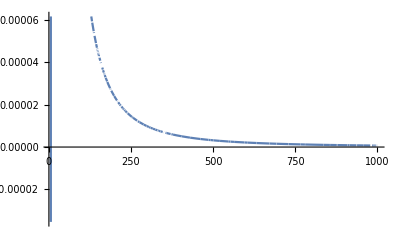

```mathematica
a=0.7;
d=0.4;
Plot[ARF1d0full[n,a,d],{n,5,nmax}]
```

```mathematica
a=0.95;
d=0.45;
data=Reap[ListLogLogPlot[ARF1d0full[n,a,d],{n,10,nmax}, EvaluationMonitor:>Sow[{n,ARF1d0full[n,a,d]}]]][[2,1]];
Export["/Users/tphillips/Atmospheric time series/arfima1d0_closed3.txt",data,"Table"]
```

ListLogLogPlot::nonopt: Options expected (instead of {n,10,1000}) beyond position 1 in ListLogLogPlot[-(12941.7 (-0.000927235 n^2 (-1+n^2)^2 Gamma[-0.45+n] Gamma[0.55+n]+0.00039393 n «1» «1» (-2.66661 («1») Gamma[Plus[«2»]]+«1»)-«1»-20.007 (n-n^3) (-0.157572 Gamma[Plus[«2»]] (Times[«4»]+Times[«2»])+3.20881 (Times[«3»]+Times[«5»]+Times[«5»]))))/(n^3 (-1+n^2)^3 Gamma[-0.45+n] Gamma[0.55+n]),{n,10,1000},EvaluationMonitor:>Sow[{n,ARF1d0full[n,a,d]}]]. An option must be a rule or a list of rules.

Part::partw: Part 1 of {} does not exist.

/Users/tphillips/Atmospheric time series/arfima1d0_closed3.txt

```mathematica
a=0.95;
d=0.45;
data=Cases[ListLogLogPlot[{
Table[ARF1d0full[n,a,d],{n,2,nmax}]}],Line[data_]:>data,-4,1][[1]];

Export["/Users/tphillips/Atmospheric time series/arfima1d0_closed2.txt",data,"Table"]
```

General::munfl: Exp[-682.096-521.504 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-682.607-521.504 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Divide::indet: Indeterminate expression 0./0. encountered.

General::stop: Further output of Divide::indet will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

/Users/tphillips/Atmospheric time series/arfima1d0_closed2.txt

General::munfl: Exp[-682.096-521.504 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-682.607-521.504 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Divide::indet: Indeterminate expression 0./0. encountered.

General::stop: Further output of Divide::indet will be suppressed during this calculation.

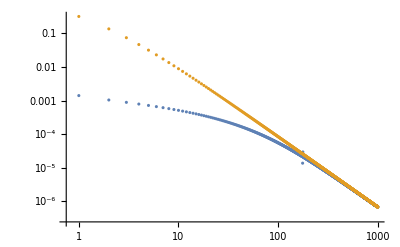

```mathematica
data=Reap[ListLogLogPlot[{
Table[ARF1d0full[n,a,d],{n,2,nmax}]},{n,10,nmax}, EvaluationMonitor:>Sow[{n,ARF1d0full[n,a,d]}]]][[2,1]];
Export["/Users/tphillips/Atmospheric time series/arfima1d0_closed.txt",data,"Table"]

ListLogLogPlot[{
Table[ARF1d0full[n,a,d],{n,2,nmax}]}]
```

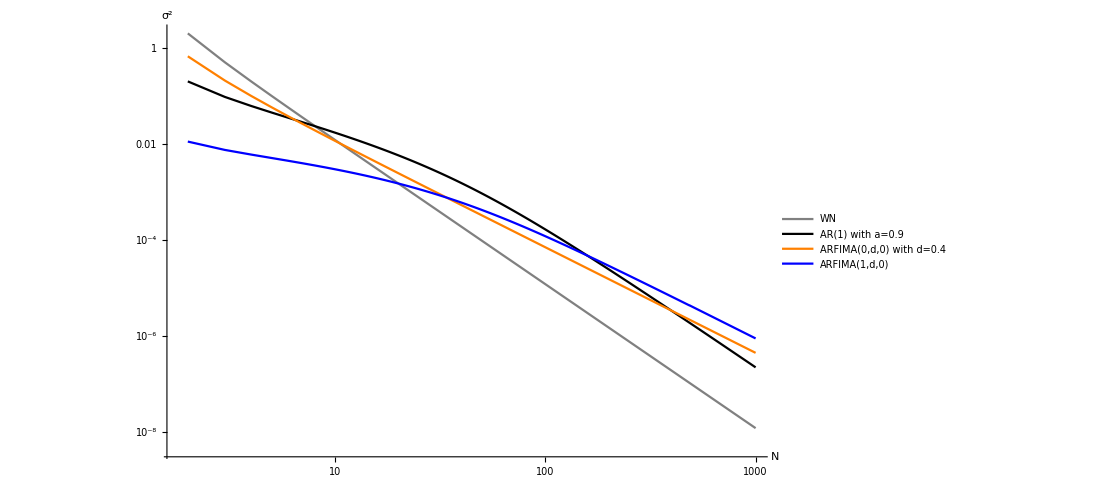

```mathematica
a=0.9;
d=0.4;
nmax=1000;
ListLogLogPlot[{
Table[WNfull[n],{n,2,nmax}],
Table[ARfull[n,a],{n,2,nmax}],
Table[ARF0d0full[n,d],{n,2,nmax}],
Table[ARF1d0full[n,a,d],{n,2,nmax}]
},
PlotLegends->Placed[{"WN","AR(1) with a=0.9","ARFIMA(0,d,0) with d=0.4","ARFIMA(1,d,0)"},{Scaled[{0.05,0.1}],{0,0}}],
PlotStyle->{Gray,Black,Orange,Blue},
Joined->True,
LabelStyle->Directive[FontSize->14,FontFamily->"FontStyle"],
DataRange->{2,nmax},
AxesLabel->{N,σ^2},
Ticks->{{1,10,100,1000},{0.0001,0.1,1}}]
Clear[a]
Clear[d]
```

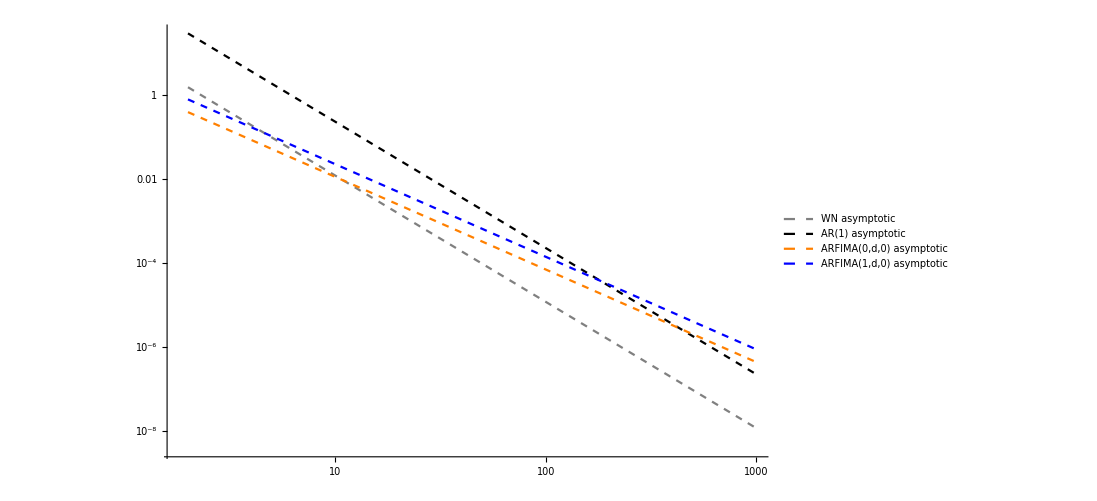

```mathematica
a=0.9;
d=0.4;
nmax=1000;
ListLogLogPlot[{
Table[WNasym[n],{n,2,nmax}],
Table[ARasym[n,a],{n,2,nmax}],
Table[ARF0d0asym[n,d],{n,2,nmax}],
Table[ARF1d0asym[n,a,d],{n,2,nmax}]
},
PlotLegends->Placed[{"WN asymptotic","AR(1) asymptotic","ARFIMA(0,d,0) asymptotic","ARFIMA(1,d,0) asymptotic"},{Scaled[{0.05,0.1}],{0,0}}],
PlotStyle->{{Gray,Dashed},{Black,Dashed},{Orange,Dashed},{Blue,Dashed}},
Joined->True,
LabelStyle->Directive[FontSize->14,FontFamily->"FontStyle"],
DataRange->{2,nmax}]
Clear[a]
Clear[d]
```

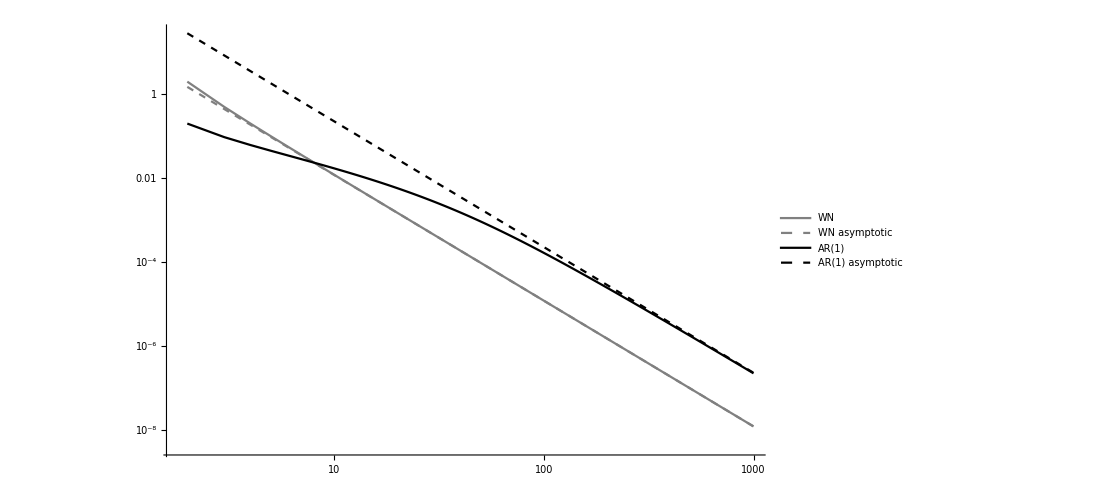

```mathematica
a=0.9;
d=0.4;
nmax=1000;
ListLogLogPlot[{
Table[WNfull[n],{n,2,nmax}],
Table[WNasym[n],{n,2,nmax}],
Table[ARfull[n,a],{n,2,nmax}],
Table[ARasym[n,a],{n,2,nmax}]
},
PlotLegends->Placed[{"WN","WN asymptotic","AR(1)","AR(1) asymptotic"},{Scaled[{0.05,0.1}],{0,0}}],
PlotStyle->{{Gray},{Gray,Dashed},{Black},{Black,Dashed}},
Joined->True,
LabelStyle->Directive[FontSize->14,FontFamily->"FontStyle"],
DataRange->{2,nmax}]
Clear[a]
Clear[d]
```

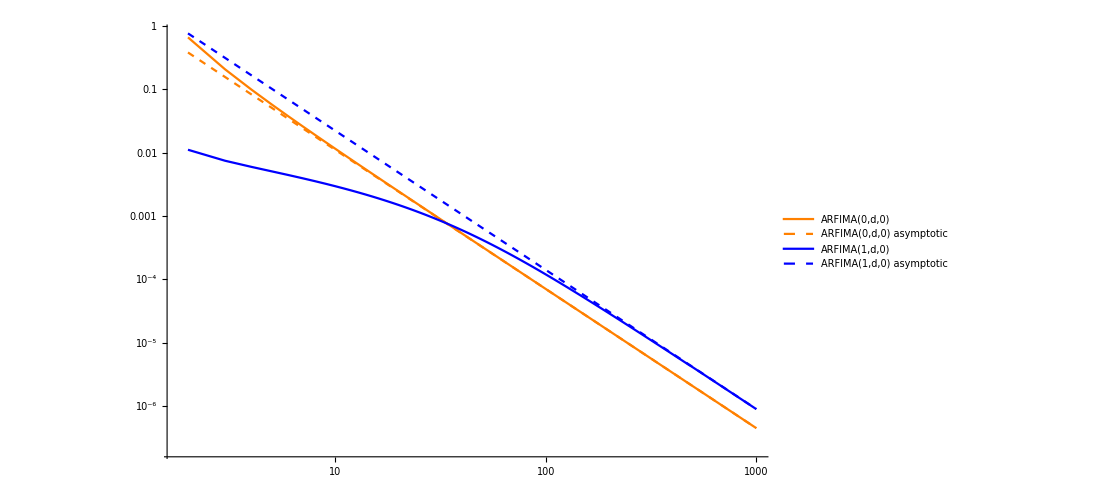

```mathematica
a=0.9;
d=0.4;
nmax=1000;
ListLogLogPlot[{
Table[ARF0d0full[n,d],{n,2,nmax}],
Table[ARF0d0asym[n,d],{n,2,nmax}],
Table[ARF1d0full[n,a,d],{n,2,nmax}],
Table[ARF1d0asym[n,a,d],{n,2,nmax}]
},
PlotLegends->Placed[{"ARFIMA(0,d,0)","ARFIMA(0,d,0) asymptotic","ARFIMA(1,d,0)","ARFIMA(1,d,0) asymptotic"},{Scaled[{0.05,0.1}],{0,0}}],
PlotStyle->{Orange,{Orange,Dashed},Blue,{Blue,Dashed}},
Joined->True,
LabelStyle->Directive[FontSize->14,FontFamily->"FontStyle"],
DataRange->{2,nmax}]
Clear[a]
Clear[d]
```

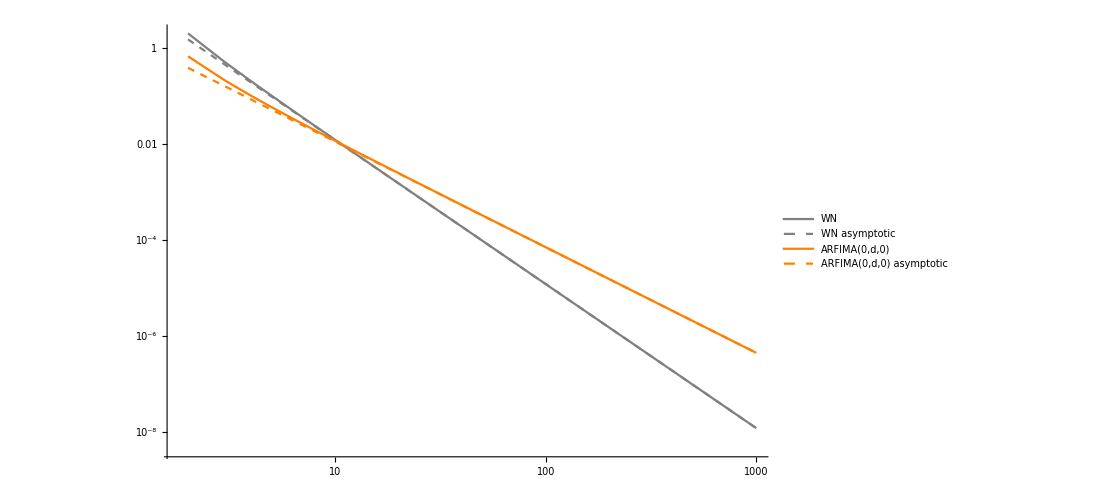

```mathematica
a=0.9;
d=0.4;
nmax=1000;
ListLogLogPlot[{
Table[WNfull[n],{n,2,nmax}],
Table[WNasym[n],{n,2,nmax}],
Table[ARF0d0full[n,d],{n,2,nmax}],
Table[ARF0d0asym[n,d],{n,2,nmax}]
},
PlotLegends->Placed[{"WN","WN asymptotic","ARFIMA(0,d,0)","ARFIMA(0,d,0) asymptotic"},{Scaled[{0.05,0.1}],{0,0}}],
PlotStyle->{Gray,{Gray,Dashed},Orange,{Orange,Dashed}},
Joined->True,
LabelStyle->Directive[FontSize->14,FontFamily->"FontStyle"],
DataRange->{2,nmax}]
Clear[a]
Clear[d]
```

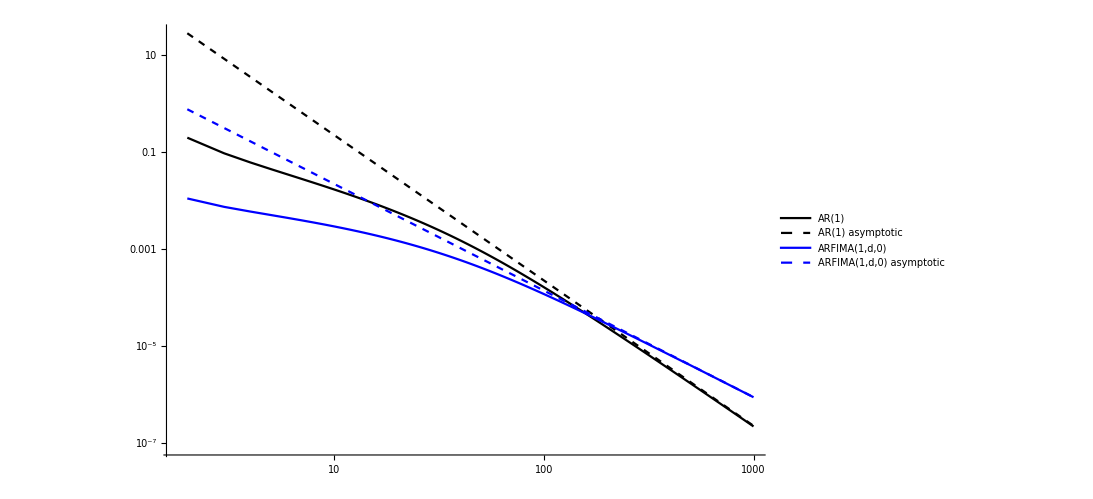

```mathematica
a=0.9;
d=0.4;
nmax=1000;
ListLogLogPlot[{
Table[ARfull[n,a],{n,2,nmax}],
Table[ARasym[n,a],{n,2,nmax}],
Table[ARF1d0full[n,a,d],{n,2,nmax}],
Table[ARF1d0asym[n,a,d],{n,2,nmax}]
},
PlotLegends->Placed[{"AR(1)","AR(1) asymptotic","ARFIMA(1,d,0)","ARFIMA(1,d,0) asymptotic"},{Scaled[{0.05,0.1}],{0,0}}],
PlotStyle->{Black,{Black,Dashed},Blue,{Blue,Dashed}},
Joined->True,
LabelStyle->Directive[FontSize->14,FontFamily->"FontStyle"],
DataRange->{2,nmax}]
Clear[a]
Clear[d]
```

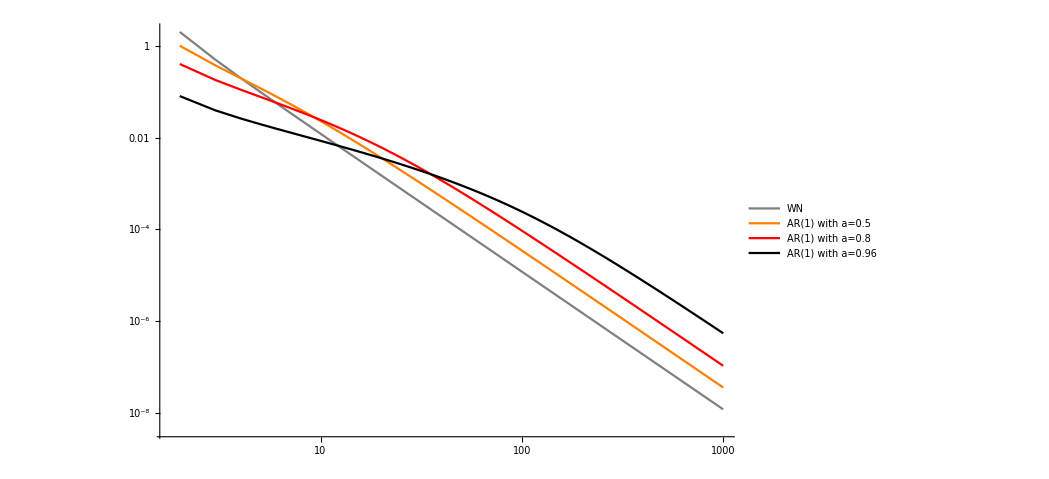

```mathematica
nmax=1000;
ListLogLogPlot[{
Table[WNfull[n],{n,2,nmax}],
Table[ARfull[n,0.5],{n,2,nmax}],
Table[ARfull[n,0.8],{n,2,nmax}],
Table[ARfull[n,0.96],{n,2,nmax}]
},
PlotLegends->Placed[{"WN","AR(1) with a=0.5","AR(1) with a=0.8","AR(1) with a=0.96"},{Scaled[{0.05,0.1}],{0,0}}],
PlotStyle->{Gray,Orange,Red,Black},
Joined->True,
LabelStyle->Directive[FontSize->14,FontFamily->"FontStyle"],
DataRange->{2,nmax}]
Clear[a]
Clear[d]
```

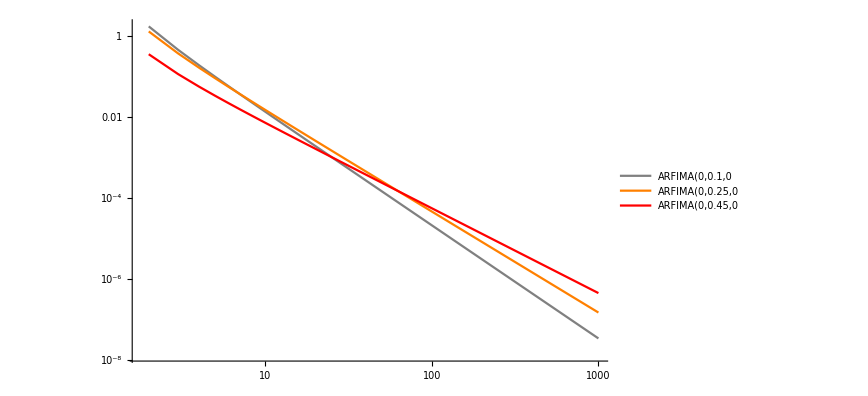

```mathematica
a=0.9;
d=0.4;
nmax=1000;
ListLogLogPlot[{
Table[ARF0d0full[n,0.1],{n,2,nmax}],
Table[ARF0d0full[n,0.25],{n,2,nmax}],
Table[ARF0d0full[n,0.45],{n,2,nmax}]
},
PlotLegends->Placed[{"ARFIMA(0,0.1,0","ARFIMA(0,0.25,0","ARFIMA(0,0.45,0"},{Scaled[{0.05,0.1}],{0,0}}],
PlotStyle->{Gray,Orange,Red},
Joined->True,
LabelStyle->Directive[FontSize->14,FontFamily->"FontStyle"],
DataRange->{2,nmax}]
Clear[a]
Clear[d]
```

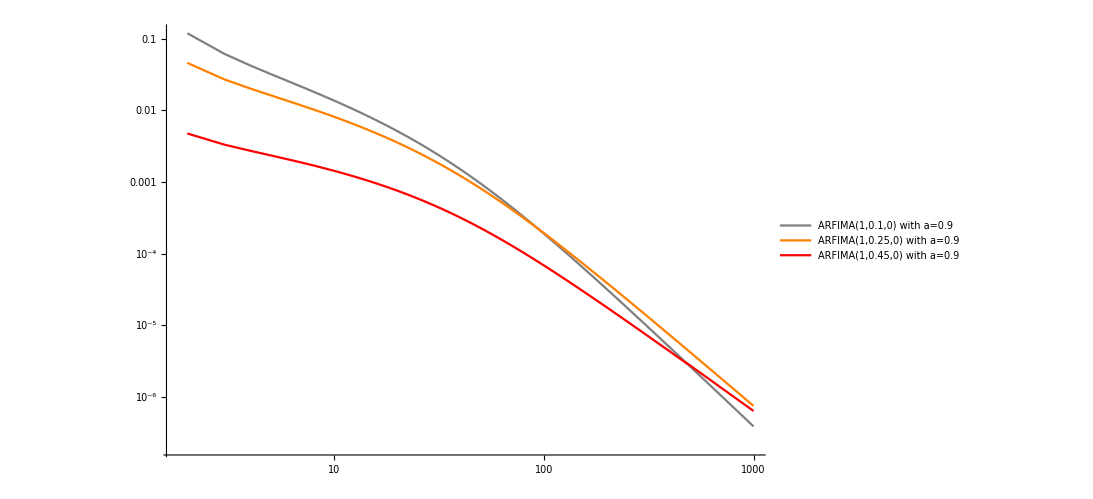

```mathematica
a=0.9;
d=0.4;
nmax=1000;
ListLogLogPlot[{
Table[ARF1d0full[n,0.9,0.1],{n,2,nmax}],
Table[ARF1d0full[n,0.9,0.25],{n,2,nmax}],
Table[ARF1d0full[n,0.9,0.45],{n,2,nmax}]
},
PlotLegends->Placed[{"ARFIMA(1,0.1,0) with a=0.9","ARFIMA(1,0.25,0) with a=0.9","ARFIMA(1,0.45,0) with a=0.9"},{Scaled[{0.05,0.1}],{0,0}}],
PlotStyle->{Gray,Orange,Red},
Joined->True,
LabelStyle->Directive[FontSize->14,FontFamily->"FontStyle"],
DataRange->{2,nmax}]
Clear[a]
Clear[d]
```

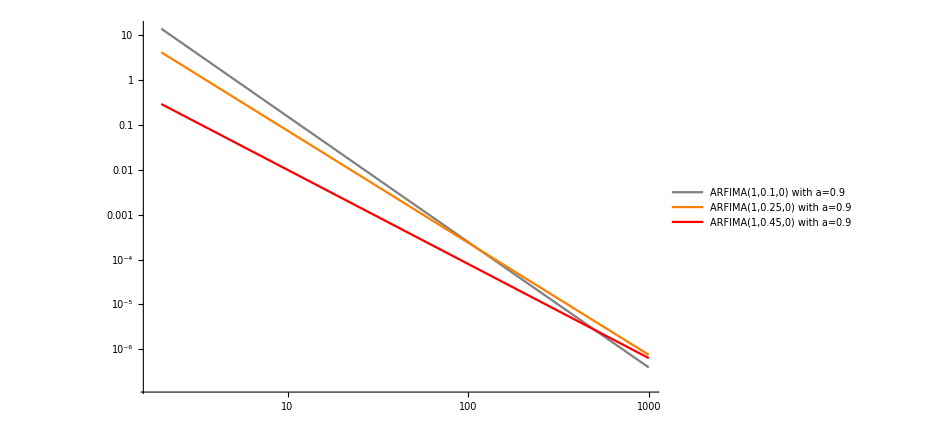

```mathematica
a=0.9;
d=0.4;
nmax=1000;
ListLogLogPlot[{
Table[ARF1d0asym[n,0.9,0.1],{n,2,nmax}],
Table[ARF1d0asym[n,0.9,0.25],{n,2,nmax}],
Table[ARF1d0asym[n,0.9,0.45],{n,2,nmax}]
},
PlotLegends->Placed[{"ARFIMA(1,0.1,0) with a=0.9","ARFIMA(1,0.25,0) with a=0.9","ARFIMA(1,0.45,0) with a=0.9"},{Scaled[{0.05,0.1}],{0,0}}],
PlotStyle->{Gray,Orange,Red},
Joined->True,
LabelStyle->Directive[FontSize->14,FontFamily->"FontStyle"],
DataRange->{2,nmax}]
Clear[a]
Clear[d]
```

```mathematica
ARF1d0asym[d_]:=(-(18 ((-1+a^2) (1-2 d) Gamma[1-d]))/(d (1+2 d) (3+2 d) Gamma[d] (-1+2 Hypergeometric2F1[1,d,1-d,a])))*(2/(1-a)^2);
```

```mathematica
ARF1d0asym'[d]
```

(72 (-1+a^2) (1-2 d) Gamma[1-d])/((1-a)^2 d (1+2 d) (3+2 d)^2 Gamma[d] (-1+2 Hypergeometric2F1[1,d,1-d,a]))+(72 (-1+a^2) (1-2 d) Gamma[1-d])/((1-a)^2 d (1+2 d)^2 (3+2 d) Gamma[d] (-1+2 Hypergeometric2F1[1,d,1-d,a]))+(36 (-1+a^2) (1-2 d) Gamma[1-d])/((1-a)^2 d^2 (1+2 d) (3+2 d) Gamma[d] (-1+2 Hypergeometric2F1[1,d,1-d,a]))+(72 (-1+a^2) Gamma[1-d])/((1-a)^2 d (1+2 d) (3+2 d) Gamma[d] (-1+2 Hypergeometric2F1[1,d,1-d,a]))+(36 (-1+a^2) (1-2 d) Gamma[1-d] PolyGamma[0,1-d])/((1-a)^2 d (1+2 d) (3+2 d) Gamma[d] (-1+2 Hypergeometric2F1[1,d,1-d,a]))+(36 (-1+a^2) (1-2 d) Gamma[1-d] PolyGamma[0,d])/((1-a)^2 d (1+2 d) (3+2 d) Gamma[d] (-1+2 Hypergeometric2F1[1,d,1-d,a]))+(72 (-1+a^2) (1-2 d) Gamma[1-d] (-Hypergeometric2F1^(0,0,1,0)[1,d,1-d,a]+Hypergeometric2F1^(0,1,0,0)[1,d,1-d,a]))/((1-a)^2 d (1+2 d) (3+2 d) Gamma[d] (-1+2 Hypergeometric2F1[1,d,1-d,a])^2)

```mathematica
deriv[a_,d_]=(72 (-1+a^2) (1-2 d) Gamma[1-d])/((1-a)^2 d (1+2 d) (3+2 d)^2 Gamma[d] (-1+2 Hypergeometric2F1[1,d,1-d,a]))+(72 (-1+a^2) (1-2 d) Gamma[1-d])/((1-a)^2 d (1+2 d)^2 (3+2 d) Gamma[d] (-1+2 Hypergeometric2F1[1,d,1-d,a]))+(36 (-1+a^2) (1-2 d) Gamma[1-d])/((1-a)^2 d^2 (1+2 d) (3+2 d) Gamma[d] (-1+2 Hypergeometric2F1[1,d,1-d,a]))+(72 (-1+a^2) Gamma[1-d])/((1-a)^2 d (1+2 d) (3+2 d) Gamma[d] (-1+2 Hypergeometric2F1[1,d,1-d,a]))+(36 (-1+a^2) (1-2 d) Gamma[1-d] PolyGamma[0,1-d])/((1-a)^2 d (1+2 d) (3+2 d) Gamma[d] (-1+2 Hypergeometric2F1[1,d,1-d,a]))+(36 (-1+a^2) (1-2 d) Gamma[1-d] PolyGamma[0,d])/((1-a)^2 d (1+2 d) (3+2 d) Gamma[d] (-1+2 Hypergeometric2F1[1,d,1-d,a]))+(72 (-1+a^2) (1-2 d) Gamma[1-d] (-Derivative[0,0,1,0][Hypergeometric2F1][1,d,1-d,a]+Derivative[0,1,0,0][Hypergeometric2F1][1,d,1-d,a]))/((1-a)^2 d (1+2 d) (3+2 d) Gamma[d] (-1+2 Hypergeometric2F1[1,d,1-d,a])^2)
```

(72 (-1+a^2) (1-2 d) Gamma[1-d])/((1-a)^2 d (1+2 d) (3+2 d)^2 Gamma[d] (-1+2 Hypergeometric2F1[1,d,1-d,a]))+(72 (-1+a^2) (1-2 d) Gamma[1-d])/((1-a)^2 d (1+2 d)^2 (3+2 d) Gamma[d] (-1+2 Hypergeometric2F1[1,d,1-d,a]))+(36 (-1+a^2) (1-2 d) Gamma[1-d])/((1-a)^2 d^2 (1+2 d) (3+2 d) Gamma[d] (-1+2 Hypergeometric2F1[1,d,1-d,a]))+(72 (-1+a^2) Gamma[1-d])/((1-a)^2 d (1+2 d) (3+2 d) Gamma[d] (-1+2 Hypergeometric2F1[1,d,1-d,a]))+(36 (-1+a^2) (1-2 d) Gamma[1-d] PolyGamma[0,1-d])/((1-a)^2 d (1+2 d) (3+2 d) Gamma[d] (-1+2 Hypergeometric2F1[1,d,1-d,a]))+(36 (-1+a^2) (1-2 d) Gamma[1-d] PolyGamma[0,d])/((1-a)^2 d (1+2 d) (3+2 d) Gamma[d] (-1+2 Hypergeometric2F1[1,d,1-d,a]))+(72 (-1+a^2) (1-2 d) Gamma[1-d] (-Hypergeometric2F1^(0,0,1,0)[1,d,1-d,a]+Hypergeometric2F1^(0,1,0,0)[1,d,1-d,a]))/((1-a)^2 d (1+2 d) (3+2 d) Gamma[d] (-1+2 Hypergeometric2F1[1,d,1-d,a])^2)

```mathematica
Collect[deriv[a,d],d,Simplify]
```

(72 (-1+a^2) (1-2 d) Gamma[1-d])/((1-a)^2 d (1+2 d) (3+2 d)^2 Gamma[d] (-1+2 Hypergeometric2F1[1,d,1-d,a]))+(72 (-1+a^2) (1-2 d) Gamma[1-d])/((1-a)^2 d (1+2 d)^2 (3+2 d) Gamma[d] (-1+2 Hypergeometric2F1[1,d,1-d,a]))+(36 (-1+a^2) (1-2 d) Gamma[1-d])/((1-a)^2 d^2 (1+2 d) (3+2 d) Gamma[d] (-1+2 Hypergeometric2F1[1,d,1-d,a]))+(72 (-1+a^2) Gamma[1-d])/((1-a)^2 d (1+2 d) (3+2 d) Gamma[d] (-1+2 Hypergeometric2F1[1,d,1-d,a]))+(36 (-1+a^2) (1-2 d) Gamma[1-d] PolyGamma[0,1-d])/((1-a)^2 d (1+2 d) (3+2 d) Gamma[d] (-1+2 Hypergeometric2F1[1,d,1-d,a]))+(36 (-1+a^2) (1-2 d) Gamma[1-d] PolyGamma[0,d])/((1-a)^2 d (1+2 d) (3+2 d) Gamma[d] (-1+2 Hypergeometric2F1[1,d,1-d,a]))+(72 (-1+a^2) (1-2 d) Gamma[1-d] (-Hypergeometric2F1^(0,0,1,0)[1,d,1-d,a]+Hypergeometric2F1^(0,1,0,0)[1,d,1-d,a]))/((1-a)^2 d (1+2 d) (3+2 d) Gamma[d] (-1+2 Hypergeometric2F1[1,d,1-d,a])^2)

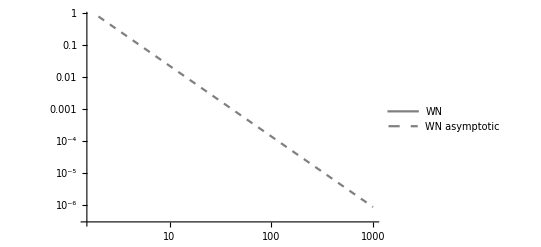

```mathematica
a=0.9;
d=0.4;
nmax=1000;
ListLogLogPlot[{
Table[deriv[n,a,d],{n,2,nmax}],
Table[ARF1d0asym[n,a,d],{n,2,nmax}]
},
PlotLegends->Placed[{"WN","WN asymptotic","AR(1)","AR(1) asymptotic","ARFIMA(0,d,0)","ARFIMA(0,d,0) asymptotic","ARFIMA(1,d,0)","ARFIMA(1,d,0) asymptotic"},{Scaled[{0.05,0.1}],{0,0}}],
PlotStyle->{Gray,{Gray,Dashed},Black,{Black,Dashed},Orange,{Orange,Dashed},Blue,{Blue,Dashed}},
Joined->True,
LabelStyle->Directive[FontSize->14,FontFamily->"FontStyle"],
DataRange->{2,nmax}]
Clear[a]
Clear[d]
```

```mathematica
a=0.807;
d=0.16;
e = 0.1;
Abs[deriv[a,d]]
```

276.532

```mathematica
ARF1d0asym[1,a,d]
```

35.2199

```mathematica
√(ARF1d0asym[1,a,d]^2 + e^2 deriv[a,d]^2)
```

44.7788

```mathematica
e = 0.04;
√(ARF1d0asym[1,a,d]^2 + e^2 deriv[a,d]^2)
```

36.916